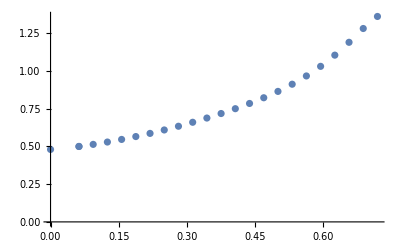

```mathematica
aa={{0,1.252321},{0.062500,1.245597},{0.062500,1.245597},{0.093750,1.246588},{0.125000,1.250118},{0.156250,1.256205},{0.187500,1.264989},{0.218750,1.276692},{0.250000,1.291590},{0.281250,1.310008},{0.312500,1.332305},{0.343750,1.358866},{0.375000,1.390086},{0.406250,1.426350},{0.437500,1.467992},{0.468750,1.515268},{0.500000,1.568362},{0.531250,1.627478},{0.562500,1.692941},{0.593750,1.765216},{0.625000,1.844909},{0.656250,1.932789},{0.687500,2.029835},{0.718750,2.137265}};
a={{0,1.732201},{0.062500,1.745196},{0.062500,1.745196},{0.093750,1.759997},{0.125000,1.779063},{0.156250,1.802409},{0.187500,1.830239},{0.218750,1.862834},{0.250000,1.900494},{0.281250,1.943496},{0.312500,1.992120},{0.343750,2.046737},{0.375000,2.107867},{0.406250,2.176155},{0.437500,2.252370},{0.468750,2.337458},{0.500000,2.432616},{0.531250,2.539356},{0.562500,2.659563},{0.593750,2.795468},{0.625000,2.949327},{0.656250,3.122243},{0.687500,3.310687},{0.718750,3.497894}};
A1=a-aa*Table[{0,1},{i,0,23}];
ListPlot[A1]
```

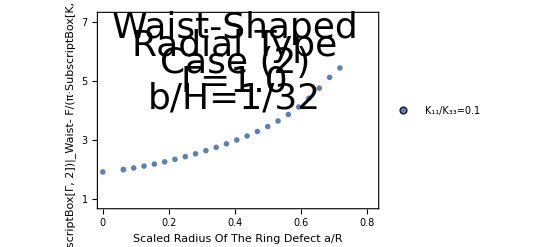

```mathematica
AA1=A1*Table[{1,4},{i,0,23}];
ListPlot[{AA1},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{1,2,3,4,5,6,7},None},{{0,0.2, 0.4, 0.6, 0.8},None}}, PlotRange->{{0,0.82},{0.8,7.2}},FrameLabel->{{"F/(π·SubscriptBox[K, 33] H SuperscriptBox[Γ, 2])|_Waist- F/(π·SubscriptBox[K, 33] H SuperscriptBox[Γ, 2])|_Cylinder", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=0.1"},LegendMarkers->{{Graphics[Disk[]],12}}],{Right, Bottom}],Epilog->{Text[Style["Waist-Shaped",Directive[Black,36]],{0.4,6.8}],Text[Style["Radial Type",Directive[Black,36]],{0.4,6.2}],Text[Style["Case (2)",Directive[Black,36]],{0.4,5.6}],Text[Style["Γ=1.0",Directive[Black,36]],{0.4,5.0}],Text[Style["b/H=1/32",Directive[Black,36]],{0.4,4.4}]}]
```